## Quantum Pendulum Potential

```mathematica
ClearAll["Global`*"]
```

Constants/Parameters

```mathematica
(*Constants (In Atomic Units)*)
m:=1
ℏ:=1
k:=1

(*Parameters*)
g:=1
l:=1
L:=3 Pi
T:=10
fps:=60
inf:=10^10
numstates:=8
```

Definitions

```mathematica
(*Potential Energy*)
V[x_]:=Piecewise[{{m g l (1-Cos[x]),-L≤x≤L }},inf];

(*Time Independent Schrodinger Equation*)
H=-(ℏ^2 ψ''[x])/(2 m l^2)+V[x] ψ[x];
```

Energy Eigenvalues/Eigenfunctions

2.42029

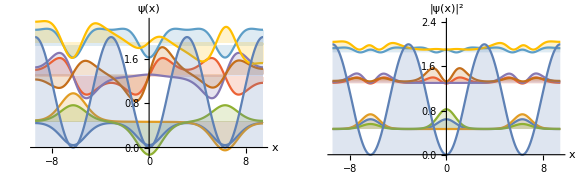

```mathematica
{vals,funs}=NDEigensystem[H,ψ[x],{x,-L,L},numstates,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];

(*Check Normalization*)
(*normfuns=Map[NIntegrate[#^2,{x,-L,L}]&,funs]*)
fillingrule:=Table[i->vals[[i]],{i,1,numstates}]
labels:=Table[ToString[Subscript[ψ, i],TraditionalForm],{i,1,numstates}]
title:=StringForm["Quantum Pendulum: First `` Stationary States",numstates]
upperbound=Max[Map[FindMaxValue[{#,-L<=x≤L},x]&,funs]]+Max[vals]

GraphicsRow[{Show[Plot[Evaluate[funs+vals],{x,-L,L},PlotRange->Full,AxesLabel->{"x","ψ(x)"},Filling->fillingrule],Plot[V[x],{x,-L,L},Filling->Axis]],Show[Plot[Evaluate[funs^2+vals],{x,-L,L},PlotRange->{0,upperbound},AxesLabel->{"x","|ψ(x)|^2"},Filling->fillingrule],Plot[V[x],{x,-L,L},Filling->Axis]]},PlotLabel->title,ImageSize->Large]
```

Stationary States

```mathematica
ϵn[n_]:=Part[vals,n];
ψn[n_]:=Part[funs,n];
Ψn[n_]:=ψn[n] Exp[-ℏ ϵn[n] t/I];
```

Mixed State

```mathematica
ψ=ψn[2]+ψn[4]-ψn[1];
Ψ=Ψn[2]+Ψn[4]-Ψn[1];

norm=Sqrt[NIntegrate[(Conjugate[ψ] ψ),{x,-L,L}]];
Ψ=Ψ/norm;
```

```mathematica
animation:=Animate[Show[Plot[Evaluate[Conjugate[Ψ] Ψ]/.t->s,{x,-L,L},Axes->True,AxesLabel->{"x","|ψ(x)|^2"},PlotRange->{0,1},PlotStyle->Red],Plot[V[x],{x,-L,L},Filling->Axis,PlotStyle->Black,Exclusions->None]],{s,0,T},DisplayAllSteps->True,DefaultDuration->T];
animation
```